#### Bulk-boundary coupling

```mathematica
Γ[q_,α_,r_]:=q/r+(√α BesselI[3/2+q,r √α])/BesselI[1/2+q,r √α];
```

#### Explanation of bulk-boundary coupling

```mathematica
ModifiedSphericalBesselI[l_,x_]:=Sqrt[Pi/2/x]BesselI[l+1/2,x];
```

```mathematica
FullSimplify[
Sqrt[α]D[ModifiedSphericalBesselI[q,x],x]/ModifiedSphericalBesselI[q,Sqrt[α]r]/.x->Sqrt[α]r,
Assumptions->α>0
]
```

q/r+(√α BesselI[3/2+q,r √α])/BesselI[1/2+q,r √α]

Problem: the coupling function Γ has σ in the denominator, which produces division by zero errors. We have to be able to filter out these cases and treat them separately.

```mathematica
Series[(√α BesselI[3/2+q,r √α])/BesselI[1/2+q,r √α],{α,0,1}]//Simplify
```

(r Gamma[3/2+q] α)/(2 Gamma[5/2+q])+O[α]^(3/2)

```mathematica
Γ0[q_,α_,r_]:=q/r+(r Gamma[3/2+q] α)/(2 Gamma[5/2+q]);
```

### Uniform chemical equilibrium

```mathematica
nSolveUniformEq[params_]:=SortBy[
DeleteDuplicates[Cases[
Chop@NSolve[
Join[memReact,cytCouple,
sphereConservedSums-r/3totalDensities
]/.params,
Join[memVars,cytVars]
],
{HoldPattern[_->(_?(Im@#==0&&#≥0&))]..}
],
Norm[#1[[All,2]]-#2[[All,2]]]<10^-5&
],
First
]
```

### Linear stability

#### Sphere geometry Jacobian

```mathematica
sphereJacobian=ArrayFlatten[{
{
D[memReact,{memVars}]-(l+1)l/r^2 DiagonalMatrix@Thread[Dm[ToString/@memVars]]-σ IdentityMatrix[Length@memVars],
D[memReact,{cytVars}]
},
{
D[cytCouple,{memVars}],
D[cytCouple,{cytVars}]-DiagonalMatrix[# Γ[l,σ/#,r]&/@bulkDiffusionConstants]
}
}];
```

#### Finding the dispersion relation

Precomputing the determinant is highly inefficient for such large systems because it includes a huge amount of terms. Calculating the determinant only on demand, from the numerical Jacobian is much faster.

```mathematica
sampleDetRoot[J_,initList_]:=
Quiet@First@MaximalBy[Check[σ/.FindRoot[Det@J,{σ,#},Evaluated->False],-100-I]&/@initList,Re]
```

```mathematica
findDispRel[params_,eq_,lMax_:10]:=With[{
JParams=sphereJacobian/.eq/.params
},
Table[
{k,sampleDetRoot[JParams/.l->k,{0.1,0.1+0.1I,1.,1.+I,3.,3.+I}]},
{k,0,lMax}
]
]
```

Use Jacobian approximation (e.g. high bulk or low bulk) as initial guess for FindRoot[].

```mathematica
findDispRel[params_,eq_,lMax_:10,
"ApproxJacobian"->(approxJ_?MatrixQ)
]:=With[{
JParams=sphereJacobian/.eq/.params,
JApproxParams=approxJ/.eq/.params
},
Table[
{lIter,
σ/.FindRoot[
Det[JParams/.l->lIter],
{σ,First@MaximalBy[Eigenvalues[JApproxParams/.l->lIter],Re]},
Evaluated->False
]
},
{lIter,0,lMax}
]
]
```

```mathematica
findHomEV[params_,eq_,"ApproxJacobian"->(approxJ_?MatrixQ)]:=With[{
JParams=sphereJacobian/.eq/.params/.l->0,
JApproxParams=approxJ/.eq/.params/.l->0
},
σ/.FindRoot[
Det[JParams],
{σ,First@MaximalBy[DeleteCases[Chop[Eigenvalues[JApproxParams]],0],Re]},
Evaluated->False
]
]
```

#### Approximate Jacobian (“well-mixed in radial direction”)

```mathematica
(*FullSimplify[Series[Γ[l,σ,r],{σ,0,2}],Assumptions->l∈Integers&&l≥0&&dC>0&&r>0]*)
```

Approximation of bulk-surface coupling for small growth rates: l/r+(r σ)/(3+2l)

```mathematica
sphereJacobianApprox=ArrayFlatten[{
{
D[memReact,{memVars}]-(l+1)l/r^2 DiagonalMatrix@Thread[Dm[ToString/@memVars]],
D[memReact,{cytVars}]
},
{
(3+2l)/r D[cytCouple,{memVars}],
(3+2l)/r D[cytCouple,{cytVars}]-l(3+2l)/r^2 DiagonalMatrix[bulkDiffusionConstants]
}
}];
```

### LSA Test

```mathematica
testEq=Last@nSolveUniformEq@Join[{r->3.5},testParams]
```

{mt→42.2523,md→10.174,mg→7.99054,mtg→27.0095,mb→17.1711,mbf→4.97687,mf→1.44919,cD→1.9122,cB→1.01599,cF→14.4919}

Slow version without using the approximated Jacobian to initialize FindRoot.

```mathematica
dispRel=findDispRel[Join[{r->3.5},testParams],testEq,10];//AbsoluteTiming
```

{0.253263,Null}

With approximated initialization.

```mathematica
dispRel=findDispRel[Join[{r->3.5},testParams],testEq,10,
"ApproxJacobian"->sphereJacobianApprox
];//AbsoluteTiming
```

{0.0286751,Null}

```mathematica
dispRel
```

{{0,3.23349×10^-16},{1,0.0611461},{2,0.0809653},{3,0.0883167},{4,0.0894064+0. ⅈ},{5,0.0864468+0. ⅈ},{6,0.0804319+0. ⅈ},{7,0.0718753+0. ⅈ},{8,0.06107+0. ⅈ},{9,0.0481951+0. ⅈ},{10,0.0333664+0. ⅈ}}

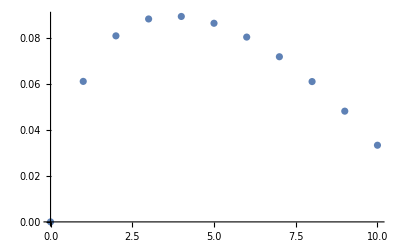

```mathematica
ListPlot[Re@dispRel]
```

The approximate Jacobian can also be used to interpolate between the discrete modes of the sphere. This might be useful in the vicinity of q_Max, e.g. to detect a non-zero imaginary part there.

```mathematica
approxDispRel=Table[{
lIter,
First@MaximalBy[
Eigenvalues[sphereJacobianApprox/.r->3.5/.testParams/.testEq/.l->lIter],
Re
]
},
{lIter,0,10,0.1}
];
```

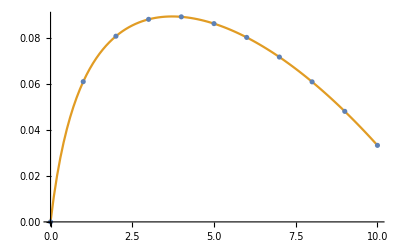

```mathematica
ListPlot[{dispRel,approxDispRel},Joined->{False,True}]
```